# CRLB for NF RADAR

```mathematica
Clear["Global`*"]
```

## Simulation Scenario

1/200

0.0025

2.0005×10^-6

0.16

10.24

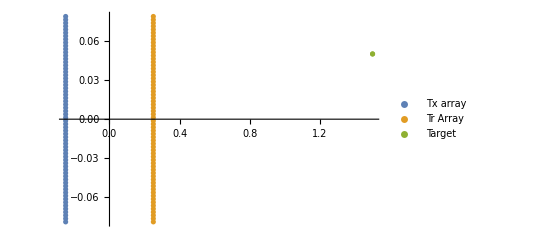

```mathematica
SeedRandom[30];
c=3 10^8; Transmitpowerdbm=20;
Ps=N[10^((Transmitpowerdbm-30)/10)];
 G=5;fc=60 10^9;
λ=c/fc

dant =N[ λ/2]
NF = 0; To = 290; K = 1.38/10^23; N0 = (10^(NF/10) )*K*To;B=1 10^9; σ = Sqrt[N0*B]
(* c1=1.69 ;c2=3.28;B=125 10^3; M=2^7;NF = 3; To = 290; K = 1.38/10^23; N0 = (10^(NF/10) )*K*To; σ = Sqrt[N0*B] ;(*σ = Sqrt[N0*B]*)
lengthscenario=10;
widthscenario=10;
xg=RandomReal[{-lengthscenario/2,lengthscenario/2},G];
yg=RandomReal[{-widthscenario/2,widthscenario/2},G];
PosG = Table[{xg[[i]], yg[[i]]}, {i, 1, G}]; *)

xu=1.5; yu=1;ζu=0.001/c;
PosU={{xu,yu}};

M=64;
lenghtant=M*dant
FD=2lenghtant^2/λ
Nr=M;
xtc=-0.25;
ytc=0;
xt=xtc*Table[1,{i,1,M}];
yt = Flatten[Table[i*dant, {i, -M/2, M/2 - 1}]] + dant/2+ytc;
pt=Table[{xt[[m]],yt[[m]]},{m,1,M}];

xrc=0.25;
yrc=0;
xr=xrc*Table[1,{i,1,Nr}];
yr = Flatten[Table[i*dant, {i, -Nr/2, Nr/2 - 1}]] + dant/2+yrc;
pr=Table[{xr[[nr]],yr[[nr]]},{nr,1,Nr}];
ListPlot[{pt,pr,PosU},PlotLegends->{"Tx array","Tr Array","Target"}]
X=Flatten[Sqrt[Ps]Table[1,{i,1,M}]/M];
RCS=1;
xu=0;
yu=0;
```

```mathematica
(*τf[x_,y_,g_]:=(√((x-xg[[g]])^2+(y-yg[[g]])^2))/c;
dgf[x_,y_,g_]:=√((x-xg[[g]])^2+(y-yg[[g]])^2); *)

dmo[m_,x_,y_]:=√((x-xt[[m]])^2+(y-yt[[m]])^2);
don[n_,x_,y_]:=√((x-xr[[n]])^2+(y-yr[[n]])^2);
dto[x_,y_]:=√((x-xtc)^2+(y-ytc)^2);
dor[x_,y_]:=√((x-xrc)^2+(y-yrc)^2);
k[x_,y_]:=√(λ^2/(dto[x,y]^2 (4π)^2) λ^2/(dor[x,y]^2 (4π)^2));
ρ[RCS_]:=√((4π)/λ^2 RCS);
κ[x_,y_]:=k[x,y] ρ[RCS];

stildekg[n_,x_,y_]:= κ[x,y]∑_(m=1)^M X[[m]]Exp[-I  (2π)/λ (dmo[m,x,y]+don[n,x,y])] ;

ytitldekg[n_,x_,y_]:=stildekg[n,x,y];

(*rhog[x_,y_,g_]:=√(10^(-(c1 Log10[dgf[x,y,g]]+c2 +2 Log10[fc])))
ytitldekg[k_,g_,x_,y_,ζ_]:=rhog[x,y,g]  stildekg[k,g,x,y,ζ];*)
ytitldeconjkg[n_,x_,y_]:=κ[x,y]∑_(m=1)^M Conjugate[X[[m]]]Exp[I  (2π)/λ (dmo[m,x,y]+don[n,x,y])]  ;
```

## CRLB Derivation

```mathematica
Γ={x,y};
ydashkg[n_,xu_,yu_]:=D[ytitldekg[n,x,y],{Γ}]/.{x->xu,y->yu};
yconjdashkg[n_,xu_,yu_]:=D[ytitldeconjkg[n,x,y],{Γ}]/.{x->xu,y->yu}; 
FIMparamvaluesf[xu_,yu_]:=2/σ^2*Sum[Re[ KroneckerProduct[ ydashkg[nr,xu,yu],yconjdashkg[nr,xu,yu] ]  ],{nr,1,Nr}];
Print["The FIM matrix of the estimated parameters= ",N[MatrixForm[FIMparamvaluesf[xu,yu]]]]
CRLBf[xu_,yu_]:=Inverse[FIMparamvaluesf[xu,yu]];
Print["The CRLB matrix of the estimated parameters= ",N[MatrixForm[CRLBf[xu,yu]]]]
PEBPos[xu_,yu_]:=N[Total[Sqrt[Diagonal[CRLBf[xu,yu]]]]]
Print["The PEB of the estimated target position= ",N[MatrixForm[PEBPos[xu,yu]]]]
PEBv=Table[{xui,PEBPos[xui,yui]},{yui,{1,2,3}},{xui,1,20,2}]
```

The FIM matrix of the estimated parameters= (3.60195×10^8 | -5.4183×10^-8
-5.4183×10^-8 | 3.1971×10^10)

The CRLB matrix of the estimated parameters= (2.77627×10^-9 | 4.7051×10^-27
4.7051×10^-27 | 3.12783×10^-11)

The PEB of the estimated target position= 0.000058283

{{{1,0.0168403},{3,0.0925108},{5,0.30003},{7,0.428667},{9,0.739628},{11,0.68319},{13,1.51821},{15,1.33883},{17,1.52603},{19,2.26675}},{{1,0.0999746},{3,0.218145},{5,0.573913},{7,1.06429},{9,1.16681},{11,2.13638},{13,2.20406},{15,2.90128},{17,4.07461},{19,5.78152}},{{1,0.850952},{3,0.559649},{5,0.755263},{7,1.39271},{9,1.7894},{11,2.96832},{13,3.29889},{15,4.6876},{17,8.7237},{19,6.38483}}}

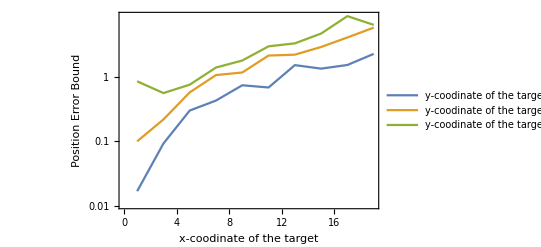

```mathematica
ListLogPlot[PEBv,Joined->True,PlotLegends->{"y-coodinate of the target=1","y-coodinate of the target=2","y-coodinate of the target=3"},FrameLabel->{"x-coodinate of the target","Position Error Bound"},Frame->True]
```